```mathematica
<<FiniteAutomata`
```

SetDelayed::write: Tag Alphabet in Alphabet[x_Automaton] is Protected.

SetDelayed::write: Tag Language in Language[auto:- Automaton -,n_Integer] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

```mathematica
A=MakeAutomaton[NDFA,{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]},{{Subscript[σ, 0],a,{Subscript[σ, 1]}},{Subscript[σ, 0],b,{Subscript[σ, 0],Subscript[σ, 1]}},{Subscript[σ, 0],c,{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]}},{Subscript[σ, 1],a,{Subscript[σ, 0]}},{Subscript[σ, 1],b,{}},{Subscript[σ, 1],c,{Subscript[σ, 1],Subscript[σ, 2]}},{Subscript[σ, 2],a,{Subscript[σ, 2]}},{Subscript[σ, 2],b,{}},{Subscript[σ, 2],c,{}}},Subscript[σ, 0],{Subscript[σ, 2]},{a,b,c}];
```

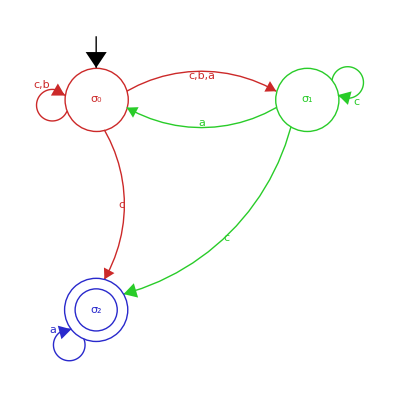

```mathematica
ShowAutomaton[A,Colored->True,Embedding->Grid]
```